```mathematica
Graphics3D[{Green,Arrowheads[0.08],Arrow[Tube[{{1,1,1},{1,1,0}},.05]],Arrow[Tube[{{2,1,1},{2,1,0}},.05]],Arrow[Tube[{{3,1,1},{3,1,0}},.05]],Arrow[Tube[{{4,1,1},{4,1,0}},.05]],Arrow[Tube[{{1,2,0},{1,2,1}},.05]],Arrow[Tube[{{2,2,0},{2,2,1}},.05]],Arrow[Tube[{{3,2,0},{3,2,1}},.05]],Arrow[Tube[{{4,2,1},{4,2,0}},.05]],Arrow[Tube[{{1,3,0},{1,3,1}}, .05]],Arrow[Tube[{{2,3,0},{2,3,1}},.05]],Arrow[Tube[{{3,3,0},{3,3,1}},.05]],Arrow[Tube[{{4,3,0},{4,3,1}},.05]],Arrow[Tube[{{1,4,0},{1,4,1}},.05]],Arrow[Tube[{{2,4,0},{2,4,1}},.05]],Arrow[Tube[{{3,4,0},{3,4,1}},.05]],Arrow[Tube[{{4,4,0},{4,4,1}},.05]],Blue,Dashed,Thickness[.01],Line[{{1,1,0.5},{2,1,0.5}}],Line[{{4,1,0.5},{4,2,0.5}}],Line[{{1,2,0.5},{1,3,0.5}}],Line[{{2,2,0.5},{3,2,0.5}}],Line[{{2,2,0.5},{2,3,0.5}}],Line[{{2,3,0.5},{2,4,0.5}}],Line[{{3,3,0.5},{3,4,0.5}}],Line[{{1,4,0.5},{2,4,0.5}}],Line[{{3,4,0.5},{4,4,0.5}}],Line[{{2,1,0.5},{3,1,0.5}}],Line[{{3,1,0.5},{4,1,0.5}}],Line[{{1,2,0.5},{2,2,0.5}}],Line[{{3,2,0.5},{3,3,0.5}}],Line[{{1,3,0.5},{2,3,0.5}}],Line[{{1,3,0.5},{1,4,0.5}}],Line[{{2,3,0.5},{3,3,0.5}}],Line[{{3,3,0.5},{4,3,0.5}}],Line[{{4,3,0.5},{4,4,0.5}}],Line[{{2,4,0.5},{3,4,0.5}}],Red,Line[{{1,1,0.5},{1,2,0.5}}],Line[{{2,1,0.5},{2,2,0.5}}],Line[{{3,1,0.5},{3,2,0.5}}],Line[{{3,2,0.5},{4,2,0.5}}],Line[{{4,2,0.5},{4,3,0.5}}],Pink, Opacity[0.5],Scale[Sphere[{3,1,0.5},0.5],{0.6,0.6,1}],Scale[Sphere[{4,3,0.5},0.5],{0.6,0.6,1}],Scale[Sphere[{4,1.5,0.5},0.5],{0.6,1.8,1.5}],Scale[Sphere[{1.5,1,0.5},0.5],{1.8,0.6,1.5}],Scale[Sphere[{1,2.5,0.5},0.5],{0.6,1.8,1.5}],Scale[Tube[BSplineCurve[{{1,4,0.5},{1.8,4,0.5},{2,4,0.5},{2,3.8,0.5},{2,2.2,0.5},{2,2,0.5},{2.2,2,0.5},{3,2,0.5}}],.4],{1,1,1.5}],Scale[Tube[BSplineCurve[{{3,3,0.5},{3,3.8,0.5},{3,4,0.5},{3.2,4,0.5},{4,4,0.5}}],.4],{1,1,1.5}],Opacity[1],Black,Text[Style["(1,1)",Large],{0.65,0.65,0.5}],Text[Style["(4,1)",Large],{4.35,0.65,0.5}],Text[Style["(1,4)",Large],{0.65,4.35,0.9}],Text[Style["(4,4)",Large],{4.35,4.35,0.9}],Purple,Text[Style[Subscript[C,1],Large],{1.5,0.45,0.5}],Text[Style[Subscript[C,2],Large],{3,0.55,0.5}],Text[Style[Subscript[C,3],Large],{4.45,1.35,0.5}],Text[Style[Subscript[C,4],Large],{0.65,2.5,1.1}],Text[Style[Subscript[C,5],Large],{1.5,4.35,1.0}],Text[Style[Subscript[C,6],Large],{4.35,3.0,0.2}],Text[Style[Subscript[C,7],Large],{3.35,4.35,1.0}]},Boxed->False]
```

-Graphics3D-

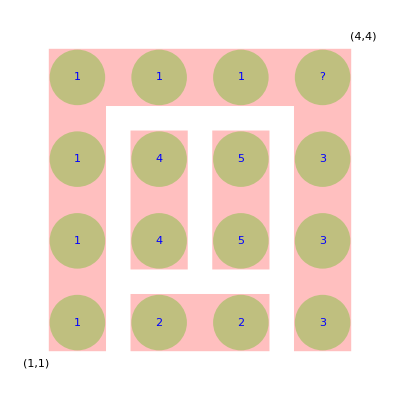

```mathematica
p=Flatten[{Table[{x,y},{x,1,4},{y,1,4}]},2];
Graphics[{PointSize[0.1],Opacity[0.5],Green,Point[p],Pink,Rectangle[{0.65,0.65},{1.35,4.35}],Rectangle[{1.35,4.35},{4.35,3.65}],Rectangle[{4.35,3.65},{3.65,0.65}],Rectangle[{1.65,0.65},{3.35,1.35}],Rectangle[{1.65,1.65},{2.35,3.35}],Rectangle[{2.65,1.65},{3.35,3.35}],Opacity[1],Blue,Text[Style["1",Large],{1,1}],Text[Style["1",Large],{1,2}],Text[Style["1",Large],{1,3}],Text[Style["1",Large],{1,4}],Text[Style["1",Large],{2,4}],Text[Style["1",Large],{3,4}],Text[Style["3",Large],{4,1}],Text[Style["3",Large],{4,2}],Text[Style["3",Large],{4,3}],Text[Style["?",Large],{4,4}],Text[Style["2",Large],{2,1}],Text[Style["2",Large],{3,1}],Text[Style["4",Large],{2,2}],Text[Style["4",Large],{2,3}],Text[Style["5",Large],{3,2}],Text[Style["5",Large],{3,3}],Black,Text[Style["(1,1)",Medium],{0.5,0.5}],Text[Style["(4,4)",Medium],{4.5,4.5}]}]
```

```mathematica
p1=Table[{Sin[theta]Cos[phi],Sin[theta]Sin[phi],Cos[theta]},{theta,Pi/6,5Pi/6,Pi/150}];
p2=Table[{Sqrt[1-z^2]Cos[phi2],Sqrt[1-z^2]Sin[phi2],z},{phi2,0,2Pi,Pi/150}];
p3={};
For[i=0,i<10^4,i++;a1=RandomReal[Pi];a2=RandomReal[2Pi];AppendTo[p3,{Sin[a1]Cos[a2],Sin[a1]Sin[a2],Cos[a1]}]];
p4={};
For[i=0,i<10^4,i++;a1=ArcCos[RandomReal[{-1,1}]];a2=RandomReal[2Pi];AppendTo[p4,{Sin[a1]Cos[a2],Sin[a1]Sin[a2],Cos[a1]}]];
Table[Graphics3D[{Sphere[],Red,Dashed,Table[Line[p1],{phi,0,2Pi,Pi/10}],Table[Line[p2],{z,-Sqrt[3]/2,Sqrt[3]/2,Sqrt[3]/10}],Black,PointSize[0.01],Point[p3]},Boxed->False,ViewPoint->vp],{vp,{{0,-Infinity,0},{0,0,Infinity}}}]
Table[Graphics3D[{Sphere[],Red,Dashed,Table[Line[p1],{phi,0,2Pi,Pi/10}],Table[Line[p2],{z,-Sqrt[3]/2,Sqrt[3]/2,Sqrt[3]/10}],Black,PointSize[0.01],Point[p4]},Boxed->False,ViewPoint->vp],{vp,{{0,-Infinity,0},{0,0,Infinity}}}]
```

{-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-}

```mathematica
Graphics3D[{Opacity[0.6],Sphere[],Purple,Polygon[{{-1.25,-1.25,0},{1.25,-1.25,0},{1.25,1.25,0},{-1.25,1.25,0}}],Opacity[1],Green,Arrowheads[0.1],Arrow[Tube[{{0,0,0},{1/Sqrt[2],0,1/Sqrt[2]}},.015]],Arrow[Tube[{{0,0,0},{0,0,1}},.015]],Arrow[Tube[{{0,0,0},{1/Sqrt[2],0,-1/Sqrt[2]}},.015]],Red,Thickness[0.01],Dashed,Line[{{1/Sqrt[2],0,-1/Sqrt[2]},{1/Sqrt[2],0,1/Sqrt[2]}}],Line[{{0,0,0},{1/Sqrt[2],0,0}}]},Boxed->False,ViewPoint->{0,-Infinity,0}]
```

-Graphics3D-

```mathematica
Graphics3D[{Green,Arrowheads[0.03],Table[a1=ArcCos[RandomReal[{0.8,1}]];a2=RandomReal[2Pi];Arrow[Tube[{{x,y,0},{x+Sin[a1]Cos[a2],y+Sin[a1]Sin[a2],Cos[a1]}},.05]],{x,1,10},{y,1,10}],Purple,Dashed,Thickness[0.002],Table[Line[{{x,1,0},{x,10,0}}],{x,1,10}],Table[Line[{{1,y,0},{10,y,0}}],{y,1,10}],Opacity[0.5],Table[Cylinder[{{x,4,0},{x,7,0}},0.12],{x,4,7}],Table[Cylinder[{{4,y,0},{7,y,0}},0.12],{y,4,7}],Cylinder[{{4,4,0},{4,3,0}},0.12],Cylinder[{{6,4,0},{6,3,0}},0.12],Cylinder[{{7,4,0},{7,3,0}},0.12],Cylinder[{{6,3,0},{7,3,0}},0.12],Cylinder[{{7,4,0},{8,4,0}},0.12],Cylinder[{{7,7,0},{8,7,0}},0.12],Cylinder[{{7,7,0},{7,8,0}},0.12],Cylinder[{{5,7,0},{5,8,0}},0.12],Cylinder[{{4,5,0},{3,5,0}},0.12],Opacity[1],Pink,Sphere[{4,3,0},0.2],Sphere[{4,4,0},0.2],Sphere[{5,4,0},0.2],Sphere[{6,3,0},0.2],Sphere[{7,3,0},0.2],Sphere[{8,4,0},0.2],Sphere[{7,5,0},0.2],Sphere[{7,6,0},0.2],Sphere[{8,7,0},0.2],Sphere[{7,8,0},0.2],Sphere[{6,7,0},0.2],Sphere[{5,8,0},0.2],Sphere[{4,7,0},0.2],Sphere[{4,6,0},0.2],Sphere[{3,5,0},0.2],Blue,Sphere[{4,2,0},0.2],Sphere[{5,3,0},0.2],Sphere[{6,2,0},0.2],Sphere[{7,2,0},0.2],Sphere[{8,3,0},0.2],Sphere[{9,4,0},0.2],Sphere[{8,5,0},0.2],Sphere[{8,6,0},0.2],Sphere[{9,7,0},0.2],Sphere[{8,8,0},0.2],Sphere[{7,9,0},0.2],Sphere[{6,8,0},0.2],Sphere[{5,9,0},0.2],Sphere[{4,8,0},0.2],Sphere[{3,7,0},0.2],Sphere[{3,6,0},0.2],Sphere[{2,5,0},0.2],Sphere[{3,4,0},0.2],Sphere[{3,3,0},0.2],Red,Thickness[0.01],Line[{{3.5,2.5,0},{4.5,2.5,0},{4.5,3.5,0},{5.5,3.5,0},{5.5,2.5,0},{7.5,2.5,0},{7.5,3.5,0},{8.5,3.5,0},{8.5,4.5,0},{7.5,4.5,0},{7.5,6.5,0},{8.5,6.5,0},{8.5,7.5,0},{7.5,7.5,0},{7.5,8.5,0},{6.5,8.5,0},{6.5,7.5,0},{5.5,7.5,0},{5.5,8.5,0},{4.5,8.5,0},{4.5,7.5,0},{3.5,7.5,0},{3.5,5.5,0},{2.5,5.5,0},{2.5,4.5,0},{3.5,4.5,0},{3.5,2.5,0}}]},Boxed->False]
```

-Graphics3D-

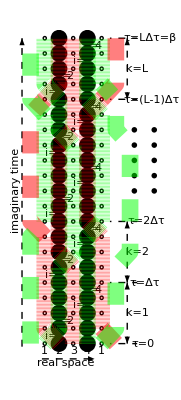

```mathematica
p1=Flatten[Table[{x,y},{x,1,5,2},{y,0,20}],1];
p2=Flatten[Table[{x,y},{x,2,4,2},{y,0,20}],1];
Graphics[{Table[Line[{{i,0},{i,20}}],{i,1,5}],Table[Line[{{Mod[4i+j,4],4i+j},{Mod[4i+j,4]+2,4i+j}}],{i,0,4},{j,1,3}],Table[{Line[{{1,j},{2,j}}],Line[{{4,j},{5,j}}]},{j,4,16,4}],Line[{{1,0},{2,0}}],Line[{{4,20},{5,20}}],PointSize[0.03],White,Point[p1],Black,Point[p2],Table[Circle[{x,y},0.11],{x,1,5,2},{y,0,20}],Dashed,Table[Line[{{5.2,j},{7.5,j}}],{j,0,8,4}],Line[{{5.2,16},{7.5,16}}],Line[{{5.2,20},{7.5,20}}],Table[Text[Style[x,Medium],{x,-0.5}],{x,1,4}],Text[Style[1,Medium],{5,-0.5}],Table[Text[Style["i=",Medium],{Mod[j,4]+1.45,j+0.5}],{j,0,19}],Table[Text[Style[Mod[j,4]+1,Medium],{Mod[j,4]+1.75,j+0.5}],{j,0,19}],Text[Style["τ=0",Medium],{7.9,0}],Text[Style["τ=Δτ",Medium],{8.0,4}],Text[Style["τ=2Δτ",Medium],{8.1,8}],Text[Style["τ=(L-1)Δτ",Medium],{8.5,16}],Text[Style["τ=LΔτ=β",Medium],{8.4,20}],Arrowheads[0.065],Arrow[{{0.8,-1},{4.5,-1}}],Arrow[{{-0.6,-0.2},{-0.6,20}}],Text[Style["real space",Medium],{2.5,-1.3}],Text[Style["imaginary time",Medium],{-1,10},Automatic,{0,1}],PointSize[0.01],Table[Point[{8.7,y}],{y,10,14}],Table[Point[{7.3,y}],{y,10,14}],Arrowheads[{-0.05,0.05}],Arrow[{{6.8,0},{6.8,4}}],Arrow[{{6.8,4},{6.8,8}}],Arrow[{{6.8,16},{6.8,20}}],Text[Style["k=1",Medium],{7.5,2}],Text[Style["k=2",Medium],{7.5,6}],Text[Style["k=L",Medium],{7.5,18}],Dashing[0],Opacity[0.5],Red,Thickness[0.03],CapForm["Round"],Line[{{2,0},{1,1},{1,7}}],Line[{{5,1},{5,7},{4,8},{4,15},{5,16}}],Line[{{1,16},{2,17},{2,20}}],Line[{{3,0},{3,5},{2,6},{2,13},{3,14},{3,20}}],Green,Line[{{1,0},{2,1},{2,5},{3,6},{3,13},{2,14},{2,16},{1,17},{1,20}}],Line[{{4,0},{4,7},{5,8},{5,15},{4,16},{4,20}}],Line[{{1,8},{1,15}}],Line[{{5,17},{5,20}}],Dashing[0.04],Red,Line[{{1,7},{0,8},{0,15},{1,16}}],Line[{{6,0},{5,1}}],Line[{{5,16},{6,17},{6,20}}],Green,Line[{{0,0},{0,7},{1,8}}],Line[{{1,15},{0,16},{0,20}}],Line[{{5,0},{6,1},{6,5},{7,6},{7,13},{6,14},{6,16},{5,17}}]},ImageSize->Scaled[.2]]
```

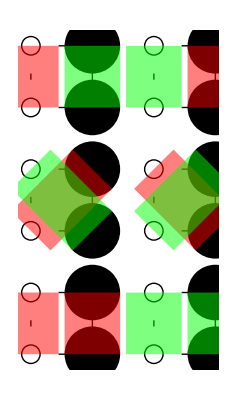

```mathematica
p1=Flatten[Table[{x,y},{x,1,3,2},{y,1,6}],1];
p2=Flatten[Table[{x,y},{x,2,4,2},{y,1,6}],1];
Graphics[{Table[Line[{{i,j},{i,j+1},{i+1,j+1},{i+1,j},{i,j}}],{i,1,3,2},{j,1,5,2}],PointSize[0.1],White,Point[p1],Black,Point[p2],Table[Circle[{i,j},0.15],{i,1,3,2},{j,1,6}],Opacity[0.5],Thickness[0.1],Red,CapForm["Round"],Line[{{1,1},{1,2}}],Line[{{2,1},{2,2}}],Line[{{1,3},{2,4}}],Line[{{3,4},{4,3}}],Line[{{1,5},{1,6}}],Line[{{4,5},{4,6}}],Green,Line[{{3,1},{3,2}}],Line[{{4,1},{4,2}}],Line[{{1,4},{2,3}}],Line[{{3,3},{4,4}}],Line[{{2,5},{2,6}}],Line[{{3,5},{3,6}}],Black,Opacity[1]}]
```

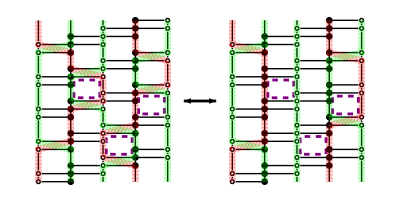

```mathematica
p1=Flatten[Table[{{0,y},{0,y+1}},{y,0,16,4}],1];
p3=Flatten[Table[{{8,y},{8,y+1},{8,y+2}},{y,1,17,4}],1];
p5=Flatten[Table[{{16,y},{16,y+1}},{y,3,19,4}],1];
p2=Flatten[Table[{{4,y},{4,y+1},{4,y+2}},{y,0,16,4}],1];
p4=Flatten[Table[{{12,y},{12,y+1},{12,y+2}},{y,2,18,4}],1];
np1=Flatten[Table[{{24,y},{24,y+1}},{y,0,16,4}],1];
np3=Flatten[Table[{{32,y},{32,y+1},{32,y+2}},{y,1,17,4}],1];
np5=Flatten[Table[{{40,y},{40,y+1}},{y,3,19,4}],1];
np2=Flatten[Table[{{28,y},{28,y+1},{28,y+2}},{y,0,16,4}],1];
np4=Flatten[Table[{{36,y},{36,y+1},{36,y+2}},{y,2,18,4}],1];
Graphics[{Table[Line[{{i,0},{i,20}}],{i,0,16,4}],Table[Line[{{i,0},{i,20}}],{i,24,40,4}],Table[Line[{{i,4j+i/4+1},{i+8,4j+i/4+1}}],{i,0,8,4},{j,0,4}],Table[Line[{{i,4j+(i-24)/4+1},{i+8,4j+(i-24)/4+1}}],{i,24,32,4},{j,0,4}],Table[{Line[{{0,j},{4,j}}],Line[{{12,j},{16,j}}]},{j,4,16,4}],Table[{Line[{{24,j},{28,j}}],Line[{{36,j},{40,j}}]},{j,4,16,4}],Line[{{0,0},{4,0}}],Line[{{12,20},{16,20}}],Line[{{24,0},{28,0}}],Line[{{36,20},{40,20}}],PointSize[0.012],White,Point[p1],Point[p3],Point[p5],Point[np1],Point[np3],Point[np5],Black,Point[p2],Point[p4],Point[np2],Point[np4],Table[Circle[p1[[i]],0.23],{i,1,Dimensions[p1,1][[1]]}],Table[Circle[p3[[i]],0.23],{i,1,Dimensions[p3,1][[1]]}],Table[Circle[p5[[i]],0.23],{i,1,Dimensions[p5,1][[1]]}],Table[Circle[np1[[i]],0.23],{i,1,Dimensions[np1,1][[1]]}],Table[Circle[np3[[i]],0.23],{i,1,Dimensions[np3,1][[1]]}],Table[Circle[np5[[i]],0.23],{i,1,Dimensions[np5,1][[1]]}],Thickness[0.005],Arrowheads[{-.03,.03}],Arrow[{{18,10},{22,10}}],Dashing[0.01],Purple,Line[{{4.4,10.4},{4.4,12.6},{7.6,12.6},{7.6,10.4},{4.4,10.4}}],Line[{{28.4,10.4},{28.4,12.6},{31.6,12.6},{31.6,10.4},{28.4,10.4}}],Line[{{8.4,3.4},{8.4,5.6},{11.6,5.6},{11.6,3.4},{8.4,3.4}}],Line[{{32.4,3.4},{32.4,5.6},{35.6,5.6},{35.6,3.4},{32.4,3.4}}],Line[{{12.4,8.4},{12.4,10.6},{15.6,10.6},{15.6,8.4},{12.4,8.4}}],Line[{{36.4,8.4},{36.4,10.6},{39.6,10.6},{39.6,8.4},{36.4,8.4}}],Dashing[0],Opacity[0.5],Thickness[0.012],CapForm["Round"],Red,Line[{{0,0},{0,4},{4,5},{4,9},{8,10},{8,13},{4,14},{4,16},{0,17},{0,20}}],Line[{{12,0},{12,2},{8,3},{8,6},{12,7},{12,11},{16,12},{16,15},{12,16},{12,20}}],Line[{{24,0},{24,4},{28,5},{28,14},{28,16},{24,17},{24,20}}],Line[{{36,0},{36,7},{40,8},{40,15},{36,16},{36,20}}],Green,Line[{{4,0},{4,4},{0,5},{0,16},{4,17},{4,20}}],Line[{{8,0},{8,2},{12,3},{12,6},{8,7},{8,9},{4,10},{4,13},{8,14},{8,20}}],Line[{{16,0},{16,11},{12,12},{12,15},{16,16},{16,20}}],Line[{{28,0},{28,4},{24,5},{24,16},{28,17},{28,20}}],Line[{{32,0},{32,20}}],Line[{{40,0},{40,7},{36,8},{36,15},{40,16},{40,20}}]},ImageSize->Scaled[.5]]
```

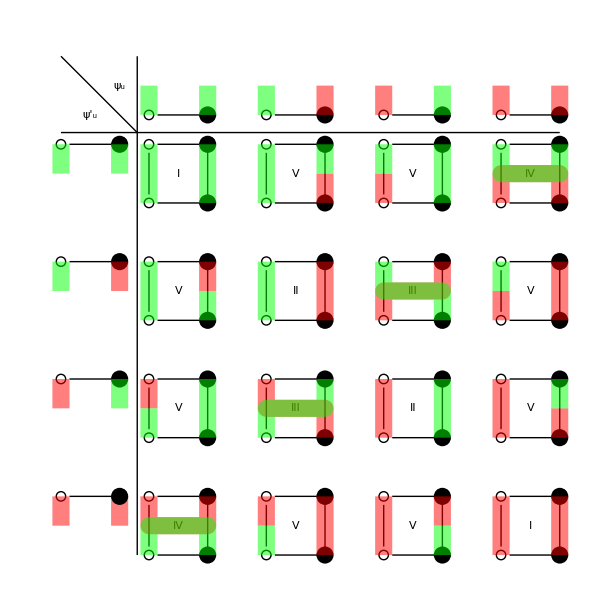

```mathematica
p1=Flatten[Table[{x,y},{x,1,7,2},{y,1,8}],1];
p3=Table[{x,8.5},{x,1,7,2}];
p5=Table[{-0.5,y},{y,2,8,2}];
p2=Flatten[Table[{x,y},{x,2,8,2},{y,1,8}],1];
p4=Table[{x,8.5},{x,2,8,2}];
p6=Table[{0.5,y},{y,2,8,2}];
Graphics[{Table[Line[{{i,j},{i,j+1},{i+1,j+1},{i+1,j},{i,j}}],{i,1,7,2},{j,1,7,2}],Line[{{-0.5,8.2},{8,8.2}}],Line[{{0.8,1},{0.8,9.5}}],Line[{{0.8,8.2},{-0.5,9.5}}],Table[Line[{{i,8.5},{i+1,8.5}}],{i,1,7,2}],Table[Line[{{-0.5,j},{0.5,j}}],{j,2,8,2}],PointSize[0.02],White,Point[p1],Point[p3],Point[p5],Black,Point[p2],Point[p4],Point[p6],Table[Circle[{i,j},0.08],{i,1,7,2},{j,1,8}],Table[Circle[{i,8.5},0.08],{i,1,7,2}],Table[Circle[{-0.5,j},0.08],{j,2,8,2}],Text[Style["ψ_u",Large],{0.5,9}],Text[Style["ψ'_u",Large],{0,8.5}],Text[Style["I",Large],{1.5,7.5}],Text[Style["I",Large],{7.5,1.5}],Text[Style["II",Large],{3.5,5.5}],Text[Style["II",Large],{5.5,3.5}],Text[Style["III",Large],{3.5,3.5}],Text[Style["III",Large],{5.5,5.5}],Text[Style["IV",Large],{1.5,1.5}],Text[Style["IV",Large],{7.5,7.5}],Text[Style["V",Large],{1.5,3.5}],Text[Style["V",Large],{1.5,5.5}],Text[Style["V",Large],{7.5,3.5}],Text[Style["V",Large],{7.5,5.5}],Text[Style["V",Large],{3.5,1.5}],Text[Style["V",Large],{3.5,7.5}],Text[Style["V",Large],{5.5,1.5}],Text[Style["V",Large],{5.5,7.5}],Opacity[0.5],Thickness[0.02],CapForm["Round"],Red,Line[{{1,2},{1,1.5},{2,1.5},{2,2}}],Line[{{3,1.5},{3,2}}],Line[{{4,1},{4,2}}],Line[{{5,1},{5,2}}],Line[{{6,1.5},{6,2}}],Line[{{7,1},{7,2}}],Line[{{8,1},{8,2}}],Line[{{1,3.5},{1,4}}],Line[{{4,3},{4,3.5},{3,3.5},{3,4}}],Line[{{5,3},{5,4}}],Line[{{7,3},{7,4}}],Line[{{8,3},{8,3.5}}],Line[{{2,5.5},{2,6}}],Line[{{4,5},{4,6}}],Line[{{5,5},{5,5.5},{6,5.5},{6,6}}],Line[{{7,5},{7,5.5}}],Line[{{8,5},{8,6}}],Line[{{4,7},{4,7.5}}],Line[{{5,7},{5,7.5}}],Line[{{7,7},{7,7.5},{8,7.5},{8,7}}],Line[{{4,8.5},{4,9}}],Line[{{5,8.5},{5,9}}],Line[{{7,8.5},{7,9}}],Line[{{8,8.5},{8,9}}],Line[{{0.5,5.5},{0.5,6}}],Line[{{-0.5,3.5},{-0.5,4}}],Line[{{-0.5,1.5},{-0.5,2}}],Line[{{0.5,1.5},{0.5,2}}],Green,Line[{{1,1},{1,1.5},{2,1.5},{2,1}}],Line[{{3,1},{3,1.5}}],Line[{{6,1},{6,1.5}}],Line[{{1,3},{1,3.5}}],Line[{{2,3},{2,4}}],Line[{{3,3},{3,3.5},{4,3.5},{4,4}}],Line[{{6,3},{6,4}}],Line[{{8,3.5},{8,4}}],Line[{{1,5},{1,6}}],Line[{{2,5},{2,5.5}}],Line[{{3,5},{3,6}}],Line[{{6,5},{6,5.5},{5,5.5},{5,6}}],Line[{{7,5.5},{7,6}}],Line[{{1,7},{1,8}}],Line[{{2,7},{2,8}}],Line[{{3,7},{3,8}}],Line[{{4,7.5},{4,8}}],Line[{{5,7.5},{5,8}}],Line[{{6,7},{6,8}}],Line[{{7,8},{7,7.5},{8,7.5},{8,8}}],Line[{{0.5,3.5},{0.5,4}}],Line[{{-0.5,5.5},{-0.5,6}}],Line[{{-0.5,7.5},{-0.5,8}}],Line[{{0.5,7.5},{0.5,8}}],Line[{{1,8.5},{1,9}}],Line[{{2,8.5},{2,9}}],Line[{{3,8.5},{3,9}}],Line[{{6,8.5},{6,9}}]}]
```

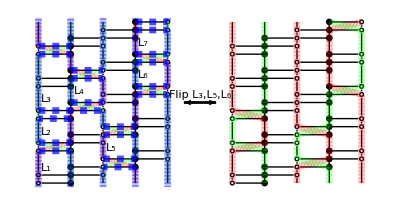

```mathematica
p1=Flatten[Table[{{0,y},{0,y+1}},{y,0,16,4}],1];
p3=Flatten[Table[{{8,y},{8,y+1},{8,y+2}},{y,1,17,4}],1];
p5=Flatten[Table[{{16,y},{16,y+1}},{y,3,19,4}],1];
p2=Flatten[Table[{{4,y},{4,y+1},{4,y+2}},{y,0,16,4}],1];
p4=Flatten[Table[{{12,y},{12,y+1},{12,y+2}},{y,2,18,4}],1];
np1=Flatten[Table[{{24,y},{24,y+1}},{y,0,16,4}],1];
np3=Flatten[Table[{{32,y},{32,y+1},{32,y+2}},{y,1,17,4}],1];
np5=Flatten[Table[{{40,y},{40,y+1}},{y,3,19,4}],1];
np2=Flatten[Table[{{28,y},{28,y+1},{28,y+2}},{y,0,16,4}],1];
np4=Flatten[Table[{{36,y},{36,y+1},{36,y+2}},{y,2,18,4}],1];
Graphics[{Table[Line[{{i,0},{i,20}}],{i,0,16,4}],Table[Line[{{i,0},{i,20}}],{i,24,40,4}],Table[Line[{{i,4j+i/4+1},{i+8,4j+i/4+1}}],{i,0,8,4},{j,0,4}],Table[Line[{{i,4j+(i-24)/4+1},{i+8,4j+(i-24)/4+1}}],{i,24,32,4},{j,0,4}],Table[{Line[{{0,j},{4,j}}],Line[{{12,j},{16,j}}]},{j,4,16,4}],Table[{Line[{{24,j},{28,j}}],Line[{{36,j},{40,j}}]},{j,4,16,4}],Line[{{0,0},{4,0}}],Line[{{12,20},{16,20}}],Line[{{24,0},{28,0}}],Line[{{36,20},{40,20}}],PointSize[0.012],White,Point[p1],Point[p3],Point[p5],Point[np1],Point[np3],Point[np5],Black,Point[p2],Point[p4],Point[np2],Point[np4],Table[Circle[p1[[i]],0.23],{i,1,Dimensions[p1,1][[1]]}],Table[Circle[p3[[i]],0.23],{i,1,Dimensions[p3,1][[1]]}],Table[Circle[p5[[i]],0.23],{i,1,Dimensions[p5,1][[1]]}],Table[Circle[np1[[i]],0.23],{i,1,Dimensions[np1,1][[1]]}],Table[Circle[np3[[i]],0.23],{i,1,Dimensions[np3,1][[1]]}],Table[Circle[np5[[i]],0.23],{i,1,Dimensions[np5,1][[1]]}],Thickness[0.005],Arrowheads[{-.03,.03}],Arrow[{{18,10},{22,10}}],Dashing[0],Opacity[0.5],Thickness[0.008],CapForm["Round"],Red,Line[{{0,0},{0,4},{4,5},{4,9},{8,10},{8,13},{4,14},{4,16},{0,17},{0,20}}],Line[{{12,0},{12,2},{8,3},{8,6},{12,7},{12,11},{16,12},{16,15},{12,16},{12,20}}],Green,Line[{{4,0},{4,4},{0,5},{0,16},{4,17},{4,20}}],Line[{{8,0},{8,2},{12,3},{12,6},{8,7},{8,9},{4,10},{4,13},{8,14},{8,20}}],Line[{{16,0},{16,11},{12,12},{12,15},{16,16},{16,20}}],Blue,Opacity[0.7],Thickness[0.012],Line[{{0,16},{0,9}}],Line[{{8,9},{8,7}}],Line[{{12,7},{12,11}}],Line[{{16,11},{16,-0.5}}],Line[{{16,20.5},{16,20}}],Line[{{12,20},{12,20.5}}],Line[{{12,-0.5},{12,2}}],Line[{{8,2},{8,-0.5}}],Line[{{8,20.5},{8,14}}],Line[{{4,14},{4,16}}],Line[{{0,8},{0,5}}],Line[{{4,5},{4,8}}],Line[{{0,-0.5},{0,4}}],Line[{{4,-0.5},{4,4}}],Line[{{0,17},{0,20.5}}],Line[{{4,17},{4,20.5}}],Line[{{4,13},{4,10}}],Line[{{8,13},{8,10}}],Line[{{12,3},{12,6}}],Line[{{8,3},{8,6}}],Line[{{12,12},{12,15}}],Line[{{12,16},{12,19}}],Line[{{16,12},{16,15}}],Line[{{16,16},{16,19}}],Dashing[0.0125],Line[{{0,16},{4,16}}],Line[{{0,9},{8,9}}],Line[{{8,7},{12,7}}],Line[{{12,11},{16,11}}],Line[{{12,20},{16,20}}],Line[{{12,2},{8,2}}],Line[{{4,14},{8,14}}],Line[{{0,5},{4,5}}],Line[{{4,8},{0,8}}],Line[{{0,4},{4,4}}],Line[{{0,17},{4,17}}],Line[{{4,13},{8,13}}],Line[{{4,10},{8,10}}],Line[{{8,3},{12,3}}],Line[{{8,6},{12,6}}],Line[{{12,12},{16,12}}],Line[{{12,15},{16,15}}],Line[{{12,16},{16,16}}],Line[{{12,19},{16,19}}],Opacity[1],Black,Text[Style["L_1",Large],{1,2}],Text[Style["L_2",Large],{1,6.5}],Text[Style["L_3",Large],{1,10.5}],Text[Style["L_4",Large],{5,11.5}],Text[Style["L_5",Large],{9,4.5}],Text[Style["L_6",Large],{13,13.5}],Text[Style["L_7",Large],{13,17.5}],Text[Style["Flip L_3,L_5,L_6",Medium],{20,11}],Dashing[0],Opacity[0.5],Thickness[0.012],Red,Line[{{24,0},{24,4},{28,5},{28,8},{24,9},{24,20}}],Line[{{32,0},{32,2},{36,3},{36,6},{32,7},{32,20}}],Line[{{40,0},{40,11},{36,12},{36,19},{40,20}}],Green,Line[{{28,0},{28,4},{24,5},{24,8},{28,9},{28,20}}],Line[{{36,0},{36,2},{32,3},{32,6},{36,7},{36,11},{40,12},{40,19},{36,20}}]},ImageSize->Scaled[.7]]
```

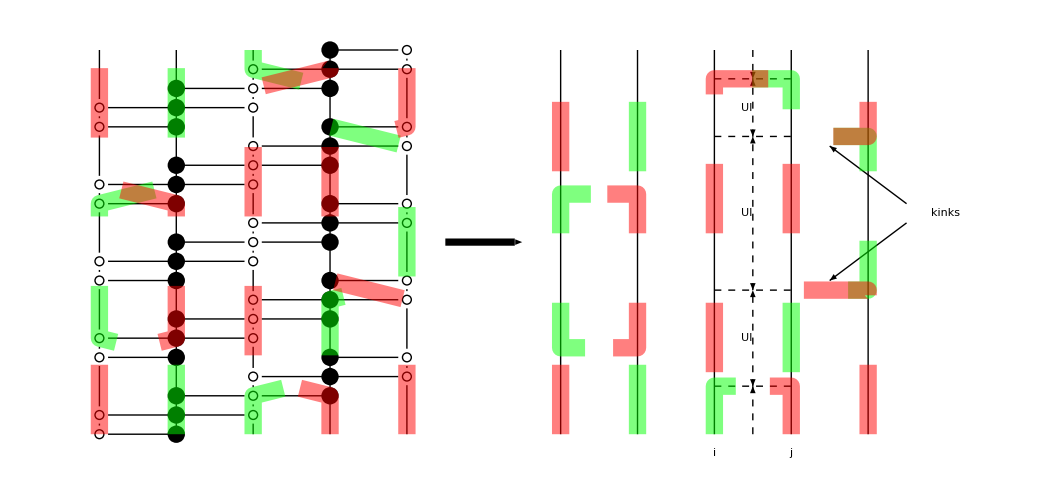

```mathematica
p1=Flatten[Table[{{0,y},{0,y+1}},{y,0,16,4}],1];
p3=Flatten[Table[{{8,y},{8,y+1},{8,y+2}},{y,1,17,4}],1];
p5=Flatten[Table[{{16,y},{16,y+1}},{y,3,19,4}],1];
p2=Flatten[Table[{{4,y},{4,y+1},{4,y+2}},{y,0,16,4}],1];
p4=Flatten[Table[{{12,y},{12,y+1},{12,y+2}},{y,2,18,4}],1];
Graphics[{Table[Line[{{i,0},{i,20}}],{i,0,16,4}],Table[Line[{{i,4j+i/4+1},{i+8,4j+i/4+1}}],{i,0,8,4},{j,0,4}],Table[{Line[{{0,j},{4,j}}],Line[{{12,j},{16,j}}]},{j,4,16,4}],Line[{{0,0},{4,0}}],Line[{{12,20},{16,20}}],Table[Line[{{i,0},{i,20}}],{i,24,40,4}],PointSize[0.012],White,Point[p1],Point[p3],Point[p5],Black,Point[p2],Point[p4],Table[Circle[p1[[i]],0.23],{i,1,Dimensions[p1,1][[1]]}],Table[Circle[p3[[i]],0.23],{i,1,Dimensions[p3,1][[1]]}],Table[Circle[p5[[i]],0.23],{i,1,Dimensions[p5,1][[1]]}],Text[Style["i",Large],{32,-1}],Text[Style["j",Large],{36,-1}],Text[Style["kinks",Large],{44,11.5}],Text[Style["UI",Large],{33.7,5}],Text[Style["UI",Large],{33.7,11.5}],Text[Style["UI",Large],{33.7,17}],Arrowheads[.03],Arrow[{{42,11},{38,8}}],Arrow[{{42,12},{38,15}}],Arrowheads[.02],Dashed,Arrow[{{34,0},{34,2.5}}],Arrow[{{34,20},{34,18.5}}],Arrowheads[{-0.02,0.02}],Arrow[{{34,2.5},{34,7.5}}],Arrow[{{34,7.5},{34,15.5}}],Arrow[{{34,15.5},{34,18.5}}],Line[{{32,2.5},{36,2.5}}],Line[{{32,7.5},{36,7.5}}],Line[{{32,15.5},{36,15.5}}],Line[{{32,18.5},{36,18.5}}],Arrowheads[.03],Thickness[0.005],Dashing[1],Arrow[{{18,10},{22,10}}],Opacity[0.5],Thickness[0.012],CapForm["Round"],Green,Line[{{4,0},{4,4},{0,5},{0,12},{4,13},{4,20}}],Line[{{8,0},{8,2},{12,3},{12,7},{16,8},{16,15},{12,16},{12,18},{8,19},{8,20}}],Line[{{28,0},{28,4.5},{24,4.5},{24,12.5},{28,12.5},{28,20}}],Line[{{32,0},{32,2.5},{36,2.5},{36,7.5},{40,7.5},{40,15.5},{36,15.5},{36,18.5},{32,18.5},{32,20}}],Red,Line[{{0,0},{0,4},{4,5},{4,12},{0,13},{0,20}}],Line[{{12,0},{12,2},{8,3},{8,18},{12,19},{12,20}}],Line[{{16,0},{16,7},{12,8},{12,15},{16,16},{16,20}}],Line[{{24,0},{24,4.5},{28,4.5},{28,12.5},{24,12.5},{24,20}}],Line[{{36,0},{36,2.5},{32,2.5},{32,18.5},{36,18.5},{36,20}}],Line[{{40,0},{40,7.5},{36,7.5},{36,15.5},{40,15.5},{40,20}}]},ImageSize->Scaled[.5]]
```

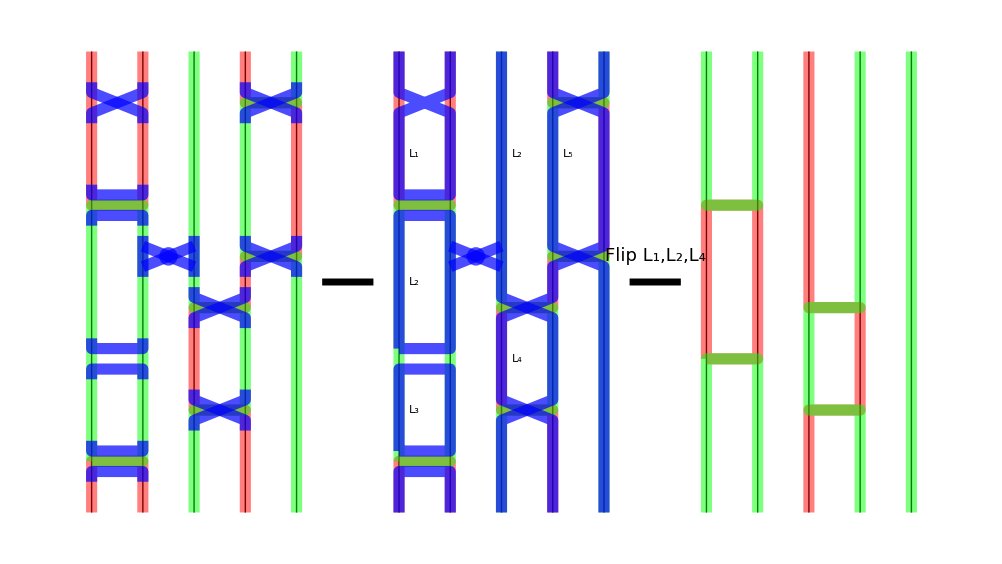

```mathematica
Graphics[{Table[Line[{{i,1},{i,10}}],{i,1,5}],Table[Line[{{i,1},{i,10}}],{i,7,11}],Table[Line[{{i,1},{i,10}}],{i,13,17}],Opacity[0.5],Thickness[0.008],CapForm["Round"],Red,Line[{{1,1},{1,2},{2,2},{2,1}}],Line[{{1,10},{1,7},{2,7},{2,10}}],Line[{{4,1},{4,3},{3,3},{3,5},{4,5},{4,6},{5,6},{5,9},{4,9},{4,10}}],Line[{{7,1},{7,2},{8,2},{8,1}}],Line[{{7,10},{7,7},{8,7},{8,10}}],Line[{{10,1},{10,3},{9,3},{9,5},{10,5},{10,6},{11,6},{11,9},{10,9},{10,10}}],Line[{{13,4},{13,7},{14,7},{14,4},{13,4}}],Line[{{15,1},{15,3},{16,3},{16,5},{15,5},{15,10}}],Green,Line[{{1,2},{2,2},{2,7},{1,7},{1,2}}],Line[{{3,1},{3,3},{4,3},{4,5},{3,5},{3,10}}],Line[{{5,1},{5,6},{4,6},{4,9},{5,9},{5,10}}],Line[{{7,2},{8,2},{8,7},{7,7},{7,2}}],Line[{{9,1},{9,3},{10,3},{10,5},{9,5},{9,10}}],Line[{{11,1},{11,6},{10,6},{10,9},{11,9},{11,10}}],Line[{{13,1},{13,4},{14,4},{14,1}}],Line[{{13,10},{13,7},{14,7},{14,10}}],Line[{{16,1},{16,3},{15,3},{15,5},{16,5},{16,10}}],Line[{{17,1},{17,10}}],Blue,Opacity[0.7],Line[{{3,3.4},{3,3.2},{4,2.8},{4,2.6}}],Line[{{3,2.6},{3,2.8},{4,3.2},{4,3.4}}],Line[{{3,5.4},{3,5.2},{4,4.8},{4,4.6}}],Line[{{3,4.6},{3,4.8},{4,5.2},{4,5.4}}],Line[{{4,5.6},{4,5.8},{5,6.2},{5,6.4}}],Line[{{4,6.4},{4,6.2},{5,5.8},{5,5.6}}],Line[{{4,8.6},{4,8.8},{5,9.2},{5,9.4}}],Line[{{4,9.4},{4,9.2},{5,8.8},{5,8.6}}],Line[{{1,2.4},{1,2.2},{2,2.2},{2,2.4}}],Line[{{1,1.6},{1,1.8},{2,1.8},{2,1.6}}],Line[{{1,6.6},{1,6.8},{2,6.8},{2,6.6}}],Line[{{1,7.4},{1,7.2},{2,7.2},{2,7.4}}],Line[{{2,5.6},{2,6.4}}],Line[{{3,5.6},{3,6.4}}],Line[{{2,5.8},{3,6.2}}],Line[{{2,6.2},{3,5.8}}],Disk[{2.5,6},0.18],Line[{{1,3.6},{1,3.8},{2,3.8},{2,3.6}}],Line[{{1,4.4},{1,4.2},{2,4.2},{2,4.4}}],Line[{{1,8.6},{1,8.8},{2,9.2},{2,9.4}}],Line[{{1,9.4},{1,9.2},{2,8.8},{2,8.6}}],Line[{{7,1},{7,1.8},{8,1.8},{8,1}}],Line[{{7,2.2},{7,3.8},{8,3.8},{8,2.2},{7,2.2}}],Line[{{7,4.2},{7,6.8},{8,6.8},{8,4.2},{7,4.2}}],Line[{{7,10},{7,9.2},{8,8.8},{8,7.2},{7,7.2},{7,8.8},{8,9.2},{8,10}}],Line[{{9,1},{9,2.8},{10,3.2},{10,4.8},{9,5.2},{9,10}}],Line[{{10,1},{10,2.8},{9,3.2},{9,4.8},{10,5.2},{10,5.8},{11,6.2},{11,8.8},{10,9.2},{10,10}}],Line[{{11,1},{11,5.8},{10,6.2},{10,8.8},{11,9.2},{11,10}}],Line[{{8,5.8},{9,6.2}}],Line[{{8,6.2},{9,5.8}}],Disk[{8.5,6},0.18],Black,Opacity[1],Thickness[0.005],Arrowheads[0.03],Arrow[{{5.5,5.5},{6.5,5.5}}],Arrow[{{11.5,5.5},{12.5,5.5}}],Text[Style["L_1",Large],{7.3,8}],Text[Style["L_2",Large],{7.3,5.5}],Text[Style["L_3",Large],{7.3,3}],Text[Style["L_2",Large],{9.3,8}],Text[Style["L_4",Large],{9.3,4}],Text[Style["L_5",Large],{10.3,8}],Text[Style["Flip L_1,L_2,L_4",FontSize->18],{12,6}]}]
```

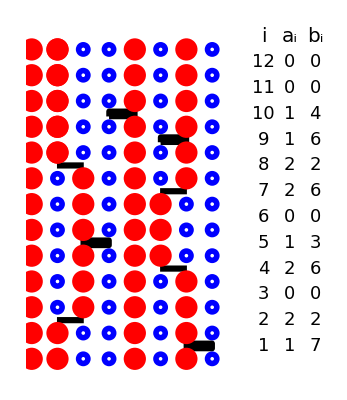

```mathematica
r=0.18;
Graphics[{PointSize[0.04],Red,Table[Point[{0,y}],{y,0,12}],Table[Point[{4,y}],{y,0,12}],Table[Point[{6,y}],{y,0,3}],Table[Point[{1,y}],{y,8,12}],Point[{{1,0},{1,1}}],Table[Point[{2,y}],{y,2,7}],Table[Point[{1,y}],{y,8,12}],Table[Point[{5,y}],{y,4,6}],Table[Point[{6,y}],{y,7,12}],Blue,Thickness[0.01],Table[Circle[{3,y},r],{y,0,12}],Table[Circle[{2,y},r],{y,0,1}],Table[Circle[{1,y},r],{y,2,7}],Table[Circle[{2,y},r],{y,8,12}],Table[Circle[{5,y},r],{y,0,3}],Table[Circle[{6,y},r],{y,4,6}],Table[Circle[{5,y},r],{y,7,12}],Table[Circle[{7,y},r],{y,0,12}],Black,Line[{{6,0.4},{6,0.6},{7,0.6},{7,0.4},{6,0.4}}],Line[{{2,4.4},{2,4.6},{3,4.6},{3,4.4},{2,4.4}}],Line[{{3,9.4},{3,9.6},{4,9.6},{4,9.4},{3,9.4}}],
Line[{{5,8.4},{5,8.6},{6,8.6},{6,8.4},{5,8.4}}],
Rectangle[{0.98,1.38},{2.02,1.62}],Rectangle[{0.98,7.38},{2.02,7.62}],Rectangle[{4.98,3.38},{6.02,3.62}],Rectangle[{4.98,6.38},{6.02,6.62}],Text[Style["i",20],{9,12.5}],Table[Text[Style[j,18],{9,j-0.5}],{j,1,12}],Text[Style["a_i",20],{10,12.5}],Text[Style["b_i",20],{11,12.5}],Text[Style["1",18],{10,0.5}],Text[Style["2",18],{10,1.5}],Text[Style["0",18],{10,2.5}],Text[Style["2",18],{10,3.5}],Text[Style["1",18],{10,4.5}],Text[Style["0",18],{10,5.5}],Text[Style["2",18],{10,6.5}],Text[Style["2",18],{10,7.5}],Text[Style["1",18],{10,8.5}],Text[Style["1",18],{10,9.5}],Text[Style["0",18],{10,10.5}],Text[Style["0",18],{10,11.5}],Text[Style["7",18],{11,0.5}],Text[Style["2",18],{11,1.5}],Text[Style["0",18],{11,2.5}],Text[Style["6",18],{11,3.5}],Text[Style["3",18],{11,4.5}],Text[Style["0",18],{11,5.5}],Text[Style["6",18],{11,6.5}],Text[Style["2",18],{11,7.5}],Text[Style["6",18],{11,8.5}],Text[Style["4",18],{11,9.5}],Text[Style["0",18],{11,10.5}],Text[Style["0",18],{11,11.5}]}]
```

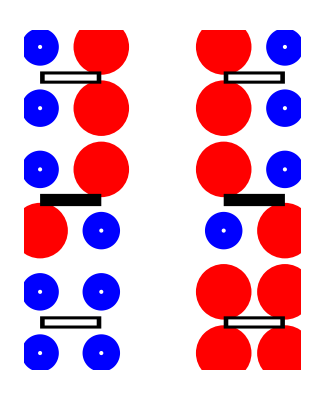

```mathematica
r=0.34;
Graphics[{PointSize[0.1],Red,Point[{{0,4},{2,6},{2,8},{2,10},{6,0},{6,2},{8,0},{8,2},{8,4},{6,6},{6,8},{6,10}}],Blue,Thickness[0.03],Circle[{0,0},r],Circle[{0,2},r],Circle[{2,0},r],Circle[{2,2},r],Circle[{0,6},r],Circle[{2,4},r],Circle[{0,8},r],Circle[{0,10},r],Circle[{6,4},r],Circle[{8,6},r],Circle[{8,8},r],Circle[{8,10},r],Black,Rectangle[{0,4.8},{2,5.2}],Rectangle[{6,4.8},{8,5.2}],Rectangle[{0,0.8},{2,1.2}],Rectangle[{0,8.8},{2,9.2}],Rectangle[{6,0.8},{8,1.2}],Rectangle[{6,8.8},{8,9.2}],White,Rectangle[{0.15,0.9},{1.85,1.1}],Rectangle[{0.15,8.9},{1.85,9.1}],Rectangle[{6.15,0.9},{7.85,1.1}],Rectangle[{6.15,8.9},{7.85,9.1}]}]
```

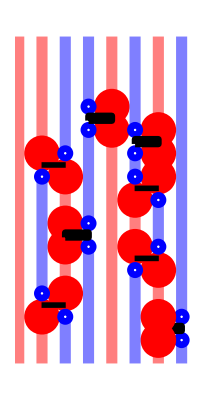

```mathematica
r=0.2;
Graphics[{PointSize[0.064],Red,Point[{{1,1},{1,8},{2,2},{2,4},{2,5},{2,7},{4,9},{4,10},{5,4},{5,6},{6,0},{6,1},{6,3},{6,7},{6,8},{6,9}}],Blue,Thickness[0.012],Circle[{1,2},r],Circle[{1,7},r],Circle[{2,1},r],Circle[{2,8},r],Circle[{3,4},r],Circle[{3,5},r],Circle[{3,9},r],Circle[{3,10},r],Circle[{5,3},r],Circle[{5,7},r],Circle[{5,8},r],Circle[{5,9},r],Circle[{6,4},r],Circle[{6,6},r],Circle[{7,0},r],Circle[{7,1},r],Black,Line[{{6,0.4},{6,0.6},{7,0.6},{7,0.4},{6,0.4}}],Line[{{2,4.4},{2,4.6},{3,4.6},{3,4.4},{2,4.4}}],Line[{{3,9.4},{3,9.6},{4,9.6},{4,9.4},{3,9.4}}],
Line[{{5,8.4},{5,8.6},{6,8.6},{6,8.4},{5,8.4}}],
Rectangle[{0.98,1.38},{2.02,1.62}],Rectangle[{0.98,7.38},{2.02,7.62}],Rectangle[{4.98,3.38},{6.02,3.62}],Rectangle[{4.98,6.38},{6.02,6.62}],Opacity[0.5],Thickness[0.02],CapForm["Round"],Red,Line[{{0,-1},{0,13}}],Line[{{4,-1},{4,9}}],Line[{{4,10},{4,13}}],Line[{{1,-1},{1,1}}],Line[{{1,8},{1,13}}],Line[{{2,2},{2,4}}],Line[{{2,5},{2,7}}],Line[{{5,4},{5,6}}],Line[{{6,-1},{6,0}}],Line[{{6,1},{6,3}}],Line[{{6,7},{6,8}}],Line[{{6,9},{6,13}}],Blue,Line[{{1,2.22},{1,6.78}}],Line[{{2,-1},{2,0.78}}],Line[{{2,8.22},{2,13}}],Line[{{3,-1},{3,3.78}}],Line[{{3,5.22},{3,8.78}}],Line[{{3,10.22},{3,13}}],Line[{{5,-1},{5,2.78}}],Line[{{5,7.22},{5,7.78}}],Line[{{5,9.22},{5,13}}],Line[{{6,4.22},{6,5.78}}],Line[{{7,-1},{7,-0.22}}],Line[{{7,1.22},{7,13}}]}]
```

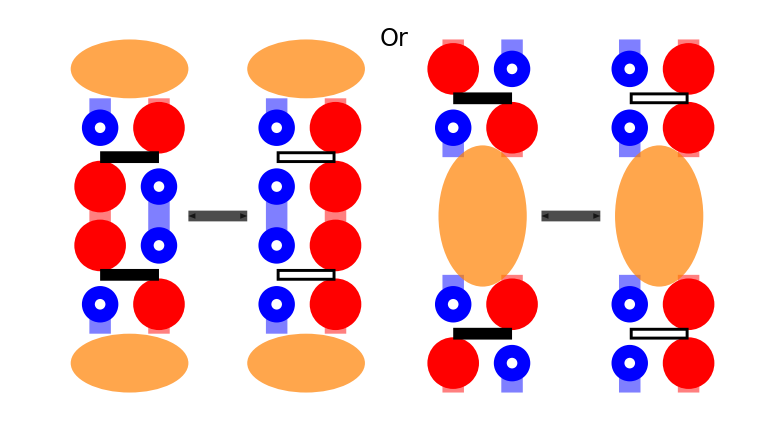

```mathematica
r=0.2;
Graphics[{PointSize[0.048],Red,Point[{{0,2},{0,3},{1,1},{1,4},{4,1},{4,2},{4,3},{4,4},{6,0},{6,5},{7,1},{7,4},{10,0},{10,1},{10,4},{10,5}}],Blue,Thickness[0.012],Circle[{0,1},r],Circle[{0,4},r],Circle[{1,2},r],Circle[{1,3},r],Table[Circle[{3,j},r],{j,1,4}],Table[{Circle[{9,j},r],Circle[{9,j+1},r]},{j,0,4,4}],Circle[{6,1},r],Circle[{6,4},r],Circle[{7,0},r],Circle[{7,5},r],Black,Rectangle[{0,1.4},{1,1.6}],Rectangle[{0,3.4},{1,3.6}],Rectangle[{6,0.4},{7,0.6}],Rectangle[{6,4.4},{7,4.6}],Rectangle[{3,1.4},{4,1.6}],Rectangle[{3,3.4},{4,3.6}],Rectangle[{9,0.4},{10,0.6}],Rectangle[{9,4.4},{10,4.6}],White,Rectangle[{3.05,1.45},{3.95,1.55}],Rectangle[{3.05,3.45},{3.95,3.55}],Rectangle[{9.05,0.45},{9.95,0.55}],Rectangle[{9.05,4.45},{9.95,4.55}],Opacity[0.5],Thickness[0.02],CapForm["Round"],Red,Line[{{0,2},{0,3}}],Line[{{4,2},{4,3}}],Line[{{1,0.5},{1,1}}],Line[{{1,4},{1,4.5}}],Line[{{4,0.5},{4,1}}],Line[{{4,4},{4,4.5}}],Line[{{6,-0.5},{6,0}}],Line[{{6,5},{6,5.5}}],Line[{{10,-0.5},{10,0}}],Line[{{10,5},{10,5.5}}],Line[{{7,1},{7,1.5}}],Line[{{7,4},{7,3.5}}],Line[{{10,1},{10,1.5}}],Line[{{10,4},{10,3.5}}],Blue,Line[{{1,2.25},{1,2.75}}],Line[{{3,2.25},{3,2.75}}],Line[{{0,0.5},{0,0.75}}],Line[{{0,4.25},{0,4.5}}],Line[{{3,0.5},{3,0.75}}],Line[{{3,4.25},{3,4.5}}],Line[{{7,-0.5},{7,-0.25}}],Line[{{7,5.25},{7,5.5}}],Line[{{9,-0.5},{9,-0.25}}],Line[{{9,5.25},{9,5.5}}],Line[{{6,1.25},{6,1.5}}],Line[{{6,3.5},{6,3.75}}],Line[{{9,1.25},{9,1.5}}],Line[{{9,3.5},{9,3.75}}],Opacity[0.7],Orange,Disk[{0.5,0},{1,0.5}],Disk[{0.5,5},{1,0.5}],Disk[{3.5,0},{1,0.5}],Disk[{3.5,5},{1,0.5}],Disk[{6.5,2.5},{0.75,1.2}],Disk[{9.5,2.5},{0.75,1.2}],Black,Thickness[0.01],Arrowheads[{-0.03,0.03}],Arrow[{{1.5,2.5},{2.5,2.5}}],Arrow[{{7.5,2.5},{8.5,2.5}}],Opacity[1],Text[Style["Or",24],{5,5.5}]}]
```

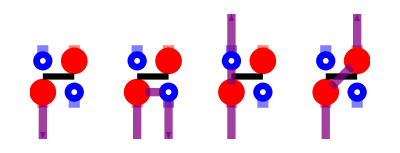

```mathematica
r=0.2;
d=0.25Sqrt[2]/2;
Graphics[{PointSize[0.048],Red,Point[{{0,1},{1,2},{3,1},{4,2},{6,1},{7,2},{9,1},{10,2}}],Blue,Thickness[0.012],Table[{Circle[{i,2},r],Circle[{i+1,1},r]},{i,0,9,3}],Black,Table[Rectangle[{i,1.4},{i+1,1.6}],{i,0,9,3}],Opacity[0.5],Thickness[0.02],CapForm["Round"],Red,Table[{Line[{{i,0.5},{i,1}}],Line[{{i+1,2},{i+1,2.5}}]},{i,0,9,3}],Blue,Table[{Line[{{i,2.25},{i,2.5}}],Line[{{i+1,0.5},{i+1,0.75}}]},{i,0,9,3}],Opacity[0.75],Purple,Thickness[0.015],Arrowheads[{-0.055,0.055}],Arrow[{{0,-0.5},{0,0.75}}],Arrowheads[0.06],Table[Arrow[{{i,-0.5},{i,0.75}}],{i,3,9,3}],Arrow[{{4,0.75},{4,-0.5}}],Arrow[{{6,2.25},{6,3.5}}],Arrow[{{10,2.25},{10,3.5}}],Line[{{3.25,1},{3.75,1}}],Line[{{6,1.25},{6,1.75}}],Line[{{9+d,1+d},{10-d,2-d}}]}]
```

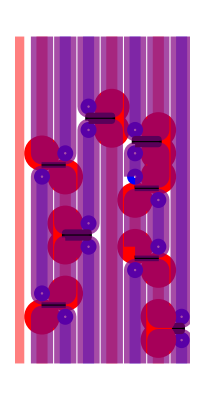

```mathematica
r=0.2;
Graphics[{PointSize[0.064],Red,Point[{{1,1},{1,8},{2,2},{2,4},{2,5},{2,7},{4,9},{4,10},{5,4},{5,6},{6,0},{6,1},{6,3},{6,7},{6,8},{6,9}}],Blue,Thickness[0.012],Circle[{1,2},r],Circle[{1,7},r],Circle[{2,1},r],Circle[{2,8},r],Circle[{3,4},r],Circle[{3,5},r],Circle[{3,9},r],Circle[{3,10},r],Circle[{5,3},r],Circle[{5,7},r],Circle[{5,8},r],Circle[{5,9},r],Circle[{6,4},r],Circle[{6,6},r],Circle[{7,0},r],Circle[{7,1},r],Black,Line[{{6,0.4},{6,0.6},{7,0.6},{7,0.4},{6,0.4}}],Line[{{2,4.4},{2,4.6},{3,4.6},{3,4.4},{2,4.4}}],Line[{{3,9.4},{3,9.6},{4,9.6},{4,9.4},{3,9.4}}],
Line[{{5,8.4},{5,8.6},{6,8.6},{6,8.4},{5,8.4}}],
Rectangle[{0.98,1.38},{2.02,1.62}],Rectangle[{0.98,7.38},{2.02,7.62}],Rectangle[{4.98,3.38},{6.02,3.62}],Rectangle[{4.98,6.38},{6.02,6.62}],Opacity[0.5],Thickness[0.02],CapForm["Round"],Red,Line[{{0,-1},{0,13}}],Line[{{4,-1},{4,9}}],Line[{{4,10},{4,13}}],Line[{{1,-1},{1,1}}],Line[{{1,8},{1,13}}],Line[{{2,2},{2,4}}],Line[{{2,5},{2,7}}],Line[{{5,4},{5,6}}],Line[{{6,-1},{6,0}}],Line[{{6,1},{6,3}}],Line[{{6,7},{6,8}}],Line[{{6,9},{6,13}}],Blue,Line[{{1,2.22},{1,6.78}}],Line[{{2,-1},{2,0.78}}],Line[{{2,8.22},{2,13}}],Line[{{3,-1},{3,3.78}}],Line[{{3,5.22},{3,8.78}}],Line[{{3,10.22},{3,13}}],Line[{{5,-1},{5,2.78}}],Line[{{5,7.22},{5,7.78}}],Line[{{5,9.22},{5,13}}],Line[{{6,4.22},{6,5.78}}],Line[{{7,-1},{7,-0.22}}],Line[{{7,1.22},{7,13}}],Opacity[0.7],Thickness[0.04],Purple,Line[{{1,-1},{1,1},{2,1},{2,-1}}],Line[{{1,13},{1,8},{2,8},{2,13}}],Line[{{3,-1},{3,4},{2,4},{2,2},{1,2},{1,7},{2,7},{2,5},{3,5},{3,9},{4,9},{4,-1}}],Line[{{3,13},{3,10},{4,10},{4,13}}],Line[{{5,-1},{5,3},{6,3},{6,1},{7,1},{7,13}}],Line[{{6,-1},{6,0},{7,0},{7,-1}}],Line[{{5,13},{5,9},{6,9},{6,13}}],Line[{{5,4},{5,6},{6,6},{6,4},{5,4}}],Line[{{5,7},{5,8},{6,8},{6,7},{5,7}}]}]
```

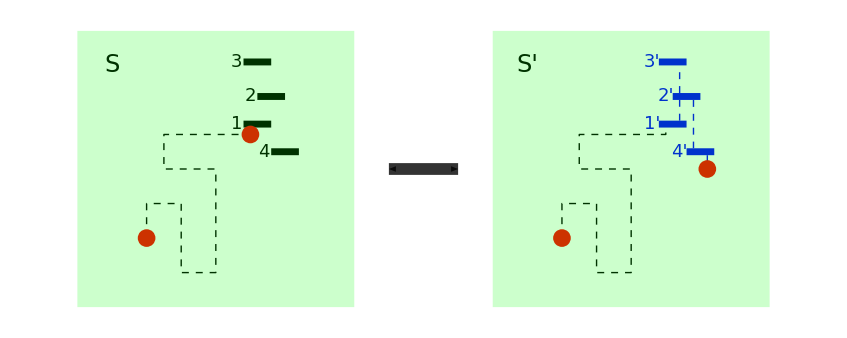

```mathematica
Graphics[{Dashed,Line[{{1,1},{1,1.5},{1.5,1.5},{1.5,0.5},{2,0.5},{2,2},{1.25,2},{1.25,2.5},{2.5,2.5}}],Line[{{7,1},{7,1.5},{7.5,1.5},{7.5,0.5},{8,0.5},{8,2},{7.25,2},{7.25,2.5},{8.5,2.5},{8.5,2.6}}],Rectangle[{2.4,2.6},{2.8,2.7}],Rectangle[{2.6,3},{3,3.1}],Rectangle[{2.4,3.5},{2.8,3.6}],Rectangle[{2.8,2.3},{3.2,2.2}],Text[Style["1",18],{2.3,2.65}],Text[Style["2",18],{2.5,3.05}],Text[Style["3",18],{2.3,3.55}],Text[Style["4",18],{2.7,2.25}],Text[Style["S",24,Italic],{0.5,3.5}],Text[Style["S'",24,Italic],{6.5,3.5}],Blue,Rectangle[{8.4,2.6},{8.8,2.7}],Line[{{8.7,2.7},{8.7,3}}],Rectangle[{8.6,3},{9,3.1}],Line[{{8.7,3.1},{8.7,3.5}}],Rectangle[{8.4,3.5},{8.8,3.6}],Line[{{8.9,3},{8.9,2.3}}],Rectangle[{8.8,2.3},{9.2,2.2}],Line[{{9.1,2.2},{9.1,2}}],Text[Style["1'",18],{8.3,2.65}],Text[Style["2'",18],{8.5,3.05}],Text[Style["3'",18],{8.3,3.55}],Text[Style["4'",18],{8.7,2.25}],Red,PointSize[0.015],Point[{{1,1},{2.5,2.5},{7,1},{9.1,2}}],Opacity[0.2],Green,Rectangle[{0,0},{4,4}],Rectangle[{6,0},{10,4}],Opacity[0.8],Dashing[1],Black,Thickness[0.01],Arrowheads[{-0.03,0.03}],Arrow[{{4.5,2},{5.5,2}}]}]
```

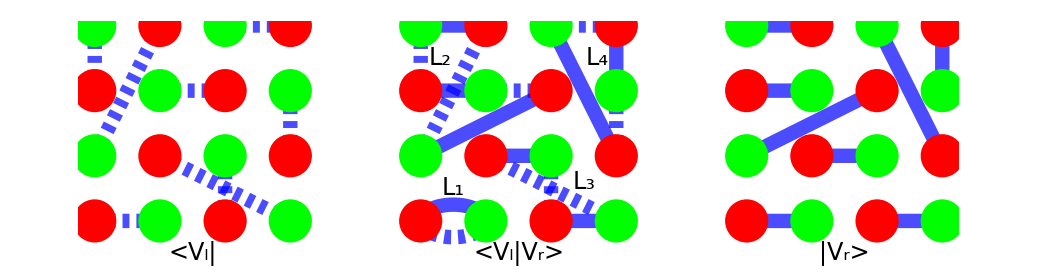

```mathematica
p1=Flatten[{Table[{x,y},{x,0,2,2},{y,0,2,2}],Table[{x,y},{x,1,3,2},{y,1,3,2}]},2];
p2=Flatten[{Table[{x,y},{x,0,2,2},{y,1,3,2}],Table[{x,y},{x,1,3,2},{y,0,2,2}]},2];
p3=Flatten[{Table[{x,y},{x,5,7,2},{y,0,2,2}],Table[{x,y},{x,6,8,2},{y,1,3,2}]},2];
p4=Flatten[{Table[{x,y},{x,5,7,2},{y,1,3,2}],Table[{x,y},{x,6,8,2},{y,0,2,2}]},2];
p5=Flatten[{Table[{x,y},{x,10,12,2},{y,0,2,2}],Table[{x,y},{x,11,13,2},{y,1,3,2}]},2];
p6=Flatten[{Table[{x,y},{x,10,12,2},{y,1,3,2}],Table[{x,y},{x,11,13,2},{y,0,2,2}]},2];
Graphics[{CapForm["Round"],Blue,Opacity[0.7],Thickness[0.01],Line[{{5,3},{6,3}}],Line[{{5,2},{6,2}}],Line[{{5,1},{7,2}}],Line[{{6,1},{7,1}}],Line[{{7,0},{8,0}}],Line[{{7,3},{8,1}}],Line[{{8,2},{8,3}}],Circle[{5.5,0},{0.5,0.25},{0,Pi}],Line[{{10,3},{11,3}}],Line[{{10,2},{11,2}}],Line[{{10,1},{12,2}}],Line[{{11,1},{12,1}}],Line[{{12,0},{13,0}}],Line[{{12,3},{13,1}}],Line[{{13,2},{13,3}}],Line[{{10,0},{11,0}}],Dashed,Line[{{5,2},{5,3}}],Line[{{5,1},{6,3}}],Line[{{6,2},{7,2}}],Line[{{6,1},{8,0}}],Line[{{7,0},{7,1}}],Line[{{8,1},{8,2}}],Line[{{7,3},{8,3}}],Circle[{5.5,0},{0.5,0.25},{0,-Pi}],Line[{{0,2},{0,3}}],Line[{{0,1},{1,3}}],Line[{{1,2},{2,2}}],Line[{{1,1},{3,0}}],Line[{{2,0},{2,1}}],Line[{{3,1},{3,2}}],Line[{{2,3},{3,3}}],Line[{{0,0},{1,0}}],Opacity[1],PointSize[0.03],Red,Point[p1],Point[p3],Point[p5],Green,Point[p2],Point[p4],Point[p6],Black,Text[Style["<V_l|",24],{1.5,-0.5}],Text[Style["|V_r>",24],{11.5,-0.5}],Text[Style["<V_l|V_r>",24],{6.5,-0.5}],Text[Style["L_1",24],{5.5,0.5}],Text[Style["L_2",24],{5.3,2.5}],Text[Style["L_3",24],{7.5,0.6}],Text[Style["L_4",24],{7.7,2.5}]}]
```

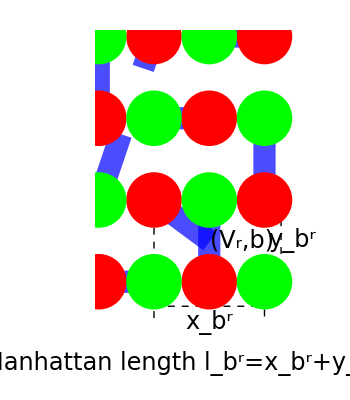

```mathematica
p1=Flatten[{Table[{x,y},{x,0,2,2},{y,0,2,2}],Table[{x,y},{x,1,3,2},{y,1,3,2}]},2];
p2=Flatten[{Table[{x,y},{x,0,2,2},{y,1,3,2}],Table[{x,y},{x,1,3,2},{y,0,2,2}]},2];
Graphics[{Dashed,Line[{{1,1},{1,-0.5}}],Line[{{1,1},{3.5,1}}],Line[{{3,0},{3,-0.5}}],Line[{{3,0},{3.5,0}}],Arrowheads[{-0.08,0.08}],Arrow[{{1,-0.3},{3,-0.3}}],Arrow[{{3.3,0},{3.3,1}}],CapForm["Round"],Blue,Opacity[0.7],Thickness[0.04],Dashing[1],Line[{{0,2},{0,3}}],Line[{{0,1},{1,3}}],Line[{{1,2},{2,2}}],Line[{{1,1},{3,0}}],Line[{{2,0},{2,1}}],Line[{{3,1},{3,2}}],Line[{{2,3},{3,3}}],Line[{{0,0},{1,0}}],Opacity[1],PointSize[0.1],Red,Point[p1],Green,Point[p2],Black,Text[Style["(V_r,b)",24],{2.6,0.5}],Text[Style["x_b^r",24],{2,-0.5}],Text[Style["y_b^r",24],{3.5,0.5}],Text[Style["Manhattan length l_b^r=x_b^r+y_b^r",24],{1.5,-1}]}]
```

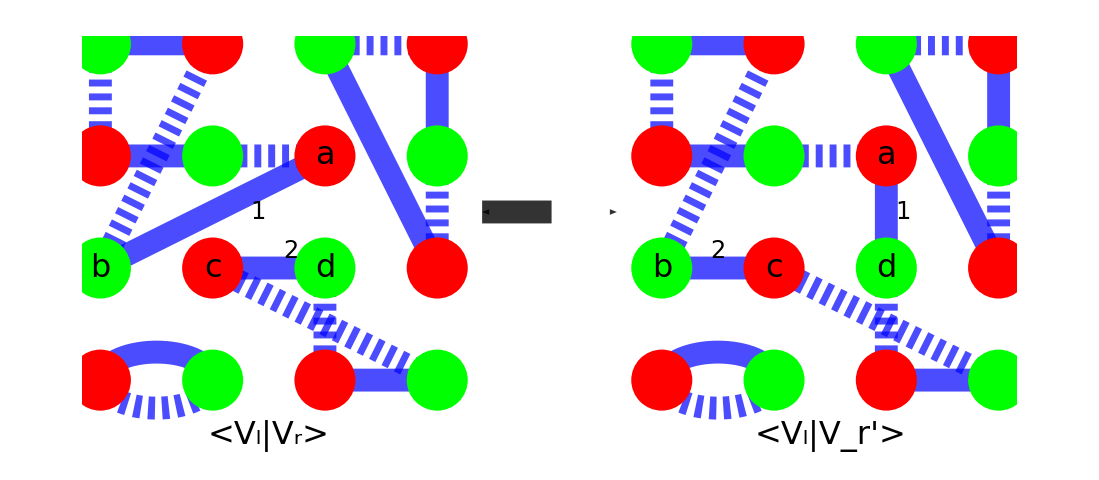

```mathematica
p1=Flatten[{Table[{x,y},{x,0,2,2},{y,0,2,2}],Table[{x,y},{x,1,3,2},{y,1,3,2}]},2];
p2=Flatten[{Table[{x,y},{x,0,2,2},{y,1,3,2}],Table[{x,y},{x,1,3,2},{y,0,2,2}]},2];
p3=Flatten[{Table[{x,y},{x,5,7,2},{y,0,2,2}],Table[{x,y},{x,6,8,2},{y,1,3,2}]},2];
p4=Flatten[{Table[{x,y},{x,5,7,2},{y,1,3,2}],Table[{x,y},{x,6,8,2},{y,0,2,2}]},2];
Graphics[{CapForm["Round"],Blue,Opacity[0.7],Thickness[0.015],Line[{{0,3},{1,3}}],Line[{{0,2},{1,2}}],Line[{{0,1},{2,2}}],Line[{{1,1},{2,1}}],Line[{{2,0},{3,0}}],Line[{{2,3},{3,1}}],Line[{{3,2},{3,3}}],Circle[{0.5,0},{0.5,0.25},{0,Pi}],Line[{{5,3},{6,3}}],Line[{{5,2},{6,2}}],Line[{{7,1},{7,2}}],Line[{{6,1},{5,1}}],Line[{{7,0},{8,0}}],Line[{{7,3},{8,1}}],Line[{{8,2},{8,3}}],Circle[{5.5,0},{0.5,0.25},{0,Pi}],Dashed,Line[{{5,2},{5,3}}],Line[{{5,1},{6,3}}],Line[{{6,2},{7,2}}],Line[{{6,1},{8,0}}],Line[{{7,0},{7,1}}],Line[{{8,1},{8,2}}],Line[{{7,3},{8,3}}],Circle[{5.5,0},{0.5,0.25},{0,-Pi}],Line[{{0,2},{0,3}}],Line[{{0,1},{1,3}}],Line[{{1,2},{2,2}}],Line[{{1,1},{3,0}}],Line[{{2,0},{2,1}}],Line[{{3,1},{3,2}}],Line[{{2,3},{3,3}}],Circle[{0.5,0},{0.5,0.25},{0,-Pi}],Opacity[1],PointSize[0.04],Red,Point[p1],Point[p3],Green,Point[p2],Point[p4],Black,Text[Style["<V_l|V_r>",32],{1.5,-0.5}],Text[Style["<V_l|V_r'>",32],{6.5,-0.5}],Text[Style["a",32],{2,2}],Text[Style["b",32],{0,1}],Text[Style["c",32],{1,1}],Text[Style["d",32],{2,1}],Text[Style["a",32],{7,2}],Text[Style["b",32],{5,1}],Text[Style["c",32],{6,1}],Text[Style["d",32],{7,1}],Text[Style["1",24],{1.4,1.5}],Text[Style["2",24],{1.7,1.15}],Text[Style["1",24],{7.15,1.5}],Text[Style["2",24],{5.5,1.15}],Dashing[1],Opacity[0.8],Arrowheads[{-0.045,0.045}],Arrow[{{3.4,1.5},{4.6,1.5}}]}]
```

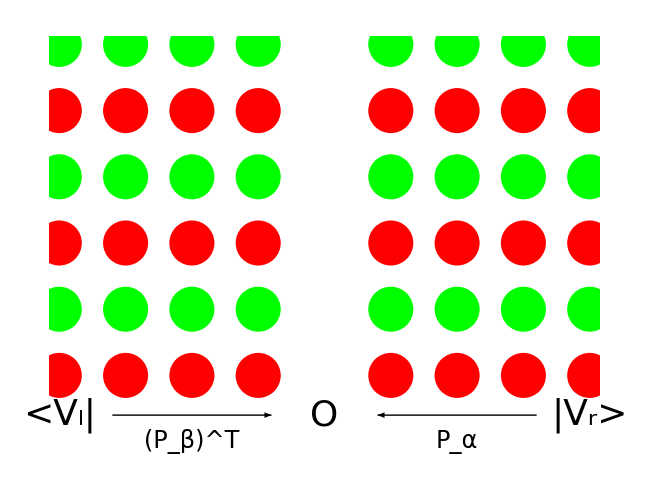

```mathematica
p1=Flatten[{Table[{x,y},{x,0,3},{y,0,4,2}],Table[{x,y},{x,5,8},{y,0,4,2}]},2];
p2=Flatten[{Table[{x,y},{x,0,3},{y,1,5,2}],Table[{x,y},{x,5,8},{y,1,5,2}]},2];
Graphics[{PointSize[0.05],Red,Point[p1],Green,Point[p2],Black,Arrowheads[0.05],Arrow[{{0.8,-0.6},{3.2,-0.6}}],Arrow[{{7.2,-0.6},{4.8,-0.6}}],Text[Style["<V_l|",36],{0,-0.6}],Text[Style["|V_r>",36],{8,-0.6}],Text[Style["O",36],{4,-0.6}],Text[Style["(P_β)^T",24],{2,-1}],Text[Style["P_α",24],{6,-1}]}]
```

```mathematica
l={{"Point",Red,{1,0,0}},{"Point",Green,{-1,0,0}},{"Point",Red,{1,0,1}},{"Point",Green,{-1,0,1}},{"Spot",White,{{1,0,2.},{0,0,0}},Pi/4,{0.55,0,0.55}},{"Spot",White,{{-1,0,2.4},{0,0,0}},Pi/4,{-0.55,0,0.55}}};
Graphics3D[{Arrowheads[0.35],Arrow[Tube[{{0,0,0},{0,0,1}},0.05]]},Lighting->l,Boxed->False]
```

-Graphics3D-

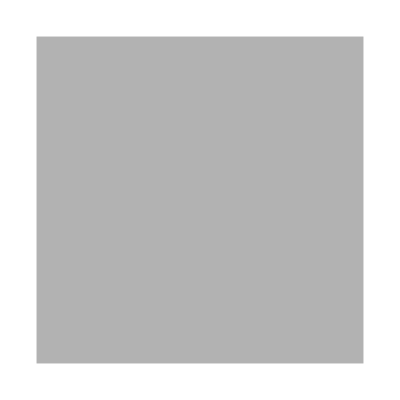

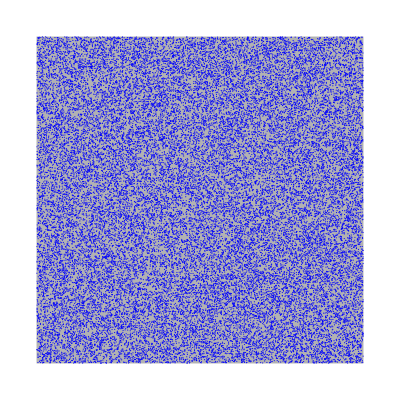

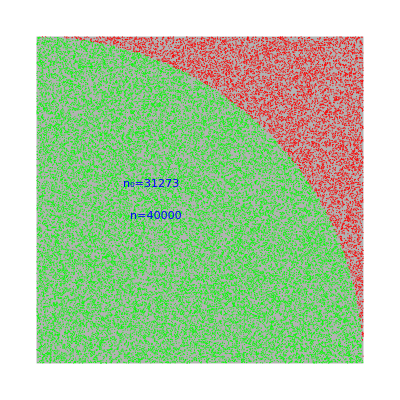

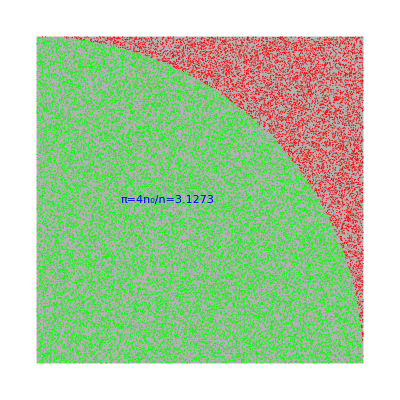

```mathematica
p={};
n=40000;
For[i=0,i<n,i++;AppendTo[p,{RandomReal[1],RandomReal[1]}]];
Graphics[{Black,Opacity[0.3],Rectangle[{-0.001,-0.001},{1.001,1.001}]}]
Graphics[{Black,Opacity[0.3],Rectangle[{-0.001,-0.001},{1.001,1.001}],Blue,Opacity[1],PointSize[0.002],Point[p]}]
pin=Select[p,#[[1]]^2+#[[2]]^2<=1 &];
n0=Length[pin];
pout=Select[p,#[[1]]^2+#[[2]]^2>1 &];
Graphics[{Black,Opacity[0.3],Rectangle[{-0.001,-0.001},{1.001,1.001}],Opacity[1],PointSize[0.002],Green,Point[pin],Red,Point[pout],Blue,Text[Style[StringJoin["n_0=",IntegerString[n0]],Large],{0.35,0.55}],Text[Style[StringJoin["n=",IntegerString[n]],Large],{0.365,0.45}]}]
Graphics[{Black,Opacity[0.3],Rectangle[{-0.001,-0.001},{1.001,1.001}],Opacity[1],PointSize[0.002],Green,Point[pin],Red,Point[pout],Blue,Text[Style[StringJoin["π=4n_0/n=",ToString[N[4*n0/n,5]]],Large],{0.4,0.5}]}]
```